# Assignment 4

### Karim Sobh 201700836

## Problem 1

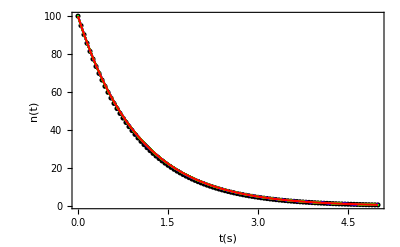

```mathematica
n[t_,n0_,τ_ ]:=n0 ⅇ^(-t/τ) (* Exact solution *)
tau =1.0;  tStart = 0.0;tMax = 5; n0 = 100;
dt = {0.05,0.001,0.0001}; (* different time steps *)

ldt = Length[dt];
color = {Black,Blue,Green};
pList = Array[plot,ldt];

Do[ (* over the values of dt *)
tList = Range[tStart,tMax,dt[[ndt]]];
lt = Length[tList];
nt = Table[0,{i,lt}];
nt[[1]] = n0;
const = (1- dt[[ndt]]/tau);

 (* Calculation *)
Do[nt[[i]] = const nt[[i-1]],{i,2,lt}]; (* Euler method *)ntList = Table[{tList[[i]],nt[[i]]},{i,lt}];

(* Results *)
plot[ndt] = ListPlot[ntList,PlotStyle->color[[ndt]]];
,{ndt,ldt}];

p2 = Plot[n[t,n0,tau ],{t,tStart,tMax},PlotStyle->Red];
Show[{pList,p2},PlotRange->All,Frame -> True,FrameLabel->{Style[t[s],Large],Style[n[t],Large]},LabelStyle->20]
```

## Problem 2

General::munfl: Exp[-1.02143×10^8] is too small to represent as a normalized machine number; precision may be lost.

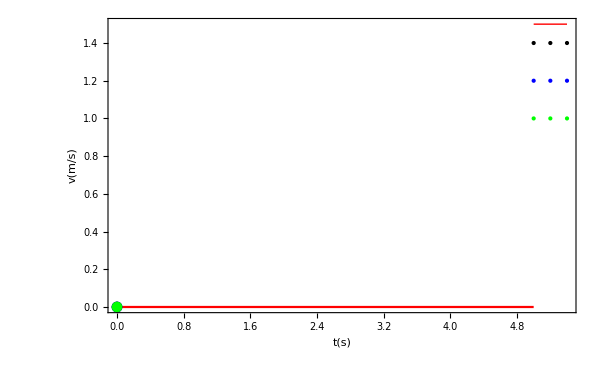

```mathematica
ClearAll[q,t,V,R,c,dt,tstart,tend];
q[t_,q0_,V_,R_,c_]:=(c V ⅇ^(-(R t)/c) (ⅇ^((R t)/c)-1))/R^2;
R= 10^6; c=10^-6; R ×c; V=10;
tstart=0; tau=1; dt = {0.1,1,0.0001}; tend=5;q0=0;ldt=Length[dt];  VR = V/R; conststep=N[tau+dt];
pList = Array[plot,ldt]; (* saves a plot for each dt *)
color = {Black,Blue,Green};  (* color for each dt plot *)
Do[tlist=Range[tstart,tend,dt[[ndt]]];lt = Length[tlist]; qlist=Table[0,{i,lt}];qlist[[1]]=q0; Do[qlist[[m]]=qlist[[m-1]]+VR ×dt -(qlist[[m-1]])/N[tau],{m,2,lt}]; tqlist=
Table[{tlist[[i]],qlist[[i]]},{i,lt}];plot[ndt] =ListPlot[tqlist,PlotStyle->color[[ndt]]]
,{ndt,Length[dt]}];
p2 = Plot[q[t,q0,V, R,c],{t,tstart,tend},PlotStyle->Red];
g1=Graphics[{Red,Line[{{5,1.5},{5.4,1.5}}]}];
g2=Graphics[{Black,PointSize[Large],Point[{{5,1.4},{5.2,1.4},{5.4,1.4}}]}];
g3=Graphics[{Blue,PointSize[Large],Point[{{5,1.2},{5.2,1.2},{5.4,1.2}}]}];
g4=Graphics[{Green,PointSize[Large],Point[{{5,1},{5.2,1},{5.4,1}}]}];Show[{pList,p2,g1,g2,g3,g4},Frame -> True,LabelStyle->20,PlotRange->All,FrameLabel->{Style["t(s)",Large],Style["v(m/s)",Large]},Epilog->{Inset[Style["Exact",17],{180,30}],
Inset[Style["dt = 8 s",17],{180,25}], Inset[Style["dt = 4 s",17] ,{180,20}],Inset[Style["dt = 1 s",17] ,{180,15}]},ImageSize->600]
```

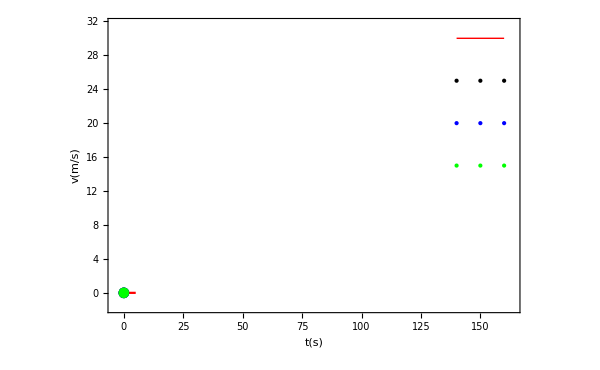

```mathematica
TraditionalForm[ ⅆq/ⅆt == (q[t + Δt] - q[t])/Δt ==V/R -q[t]/c R]
```

{{q(t)→(c V ⅇ^(-(R t)/c) (ⅇ^((R t)/c)-1))/R^2}}

{{q[t]→(c ⅇ^(-(R t)/c) (-1+ⅇ^((R t)/c)) V)/R^2}}

## Problem 3

```mathematica
Clear["Global`*"];
 color = {Black,Blue,Green,Pink,Magenta,Red};  grav = 9.8; tmax = 1000; v0 = 700;B2m =  4.0 10^-5; x0 = 0.0; y0 =0.0; 
θ=π/180.0 Range[30.,55.,5.] ;lθ = Length[θ];
p7 = Table[0,{i,lθ }]; (* Trajectory plots for diff angles *)
dt = {0.1};  ldt = Length[dt];

Do[ p5=  Table[0,{i,ldt }]; (* Trajectory plots for diff dt *)
vx0 = v0 Cos[θ[[nθ]]]; vy0 = v0 Sin[θ[[nθ]]];
Do[
tList = Range[0,1000,dt[[ndt]]]; lt = Length[tList];
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[
xList[[nt]]   = xList[[nt-1]] + vxList[[nt-1]] dt[[ndt]]; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt-1]] dt[[ndt]];
vNorm                 =  Sqrt[vxList[[nt-1]]^2+vyList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] (1.0 - B2m dt[[ndt]] vNorm);
vyList[[nt]] =vyList[[nt-1]] (1.0 - B2m dt[[ndt]] vNorm) - grav dt[[ndt]];
If[yList[[nt]]>0,nRange = nt] (* time when x = Range, y = 0 *)
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,nRange}];
p5[[ndt]] =ListPlot[xylist/1000.0,PlotStyle->color[[ndt]]],{ndt,Length[dt]}]; p7[[nθ]] =p5,{nθ,Length[θ]};
(*critical density*)
Do[
xList[[nt]]   = xList[[nt-1]] + vxList[[nt-1]] dt[[ndt]]; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt-1]] dt[[ndt]];
vNorm                 =  Sqrt[vxList[[nt-1]]^2+vyList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] (1.0 - B2m× dt[[ndt]] vNorm);
vyList[[nt]] =vyList[[nt-1]] (1.0 - B2m×dt[[ndt]] vNorm) - grav dt[[ndt]];
If[yList[[nt]]>0,nRange = nt] (* time when x = Range, y = 0 *)
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,nRange}];
p5[[ndt]] =ListPlot[xylist/1000.0,PlotStyle->color[[ndt]]],{ndt,Length[dt]}]; p7[[nθ]] =p5,{nθ,Length[θ]}


g2=Graphics[{Black,PointSize[Large],Point[{{8,2}}]}];
g3=Graphics[{Blue,PointSize[Large],Point[{{8,1.5}}]}];
g4=Graphics[{Green,PointSize[Large],Point[{{8,1}}]}];Show[p7,g2,g3,g4, PlotRange->All,Frame -> True,FrameLabel->{Style["x(km)",Large],Style["y(km)",Large]},LabelStyle->20,ImageSize->500 ,AspectRatio->1,Epilog->{Inset[Style["With drag",17] ,{20,9}], Inset[Style["35°",17] ,{13,4.8}],Inset[Style["45°",17],{13,7.2}], Inset[Style["dt = 2 s",17],{11,2}]}]
```

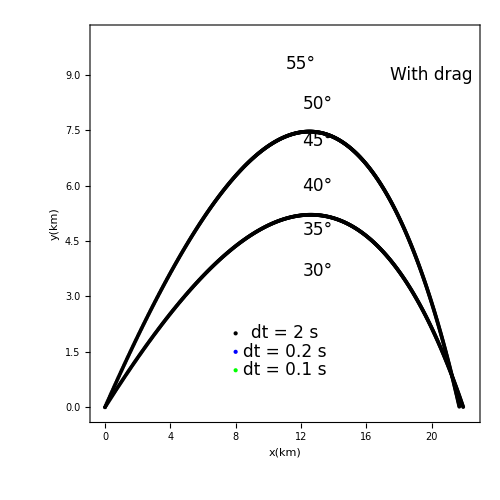

```mathematica
(* Initializations *) 
Clear["Globe `*"];
 color = {Black,Blue,Green,Pink,Magenta,Red};  
grav = 9.8;tStart = 0; tmax = 1000; v0 = 700;B2m =  4.0 10^-5; x0 = 0.0; y0 =0.0; 
θ=π/180.0 Range[30.,55.,5.] ;lθ = Length[θ];
p6 = Table[0,{i,lθ }]; (* Trajectory plots for diff angles *)
dt = {2,0.2,0.1};  ldt = Length[dt];
T0=288.15;
Do[ (* over θ *)
p5=  Table[0,{i,ldt }]; (* Trajectory plots for diff dt *)
vx0 = v0 Cos[θ[[nθ]]]; vy0 = v0 Sin[θ[[nθ]]];
Do[(* over dt *)
tList = Range[0,1000,dt[[ndt]]]; lt = Length[tList];
vxList = 0tList ; vyList = vxList; xList =vxList;yList = vxList;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[(* over tList *)
xList[[nt]]   = xList[[nt-1]] + vxList[[nt-1]] dt[[ndt]]; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt-1]] dt[[ndt]];
vNorm                 =  Sqrt[vxList[[nt-1]]^2+vyList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] (1.0 - B2m×(1-(6.5×10^{-3}/288.15)) dt[[ndt]] vNorm);
vyList[[nt]] =vyList[[nt-1]] (1.0 - B2m ×(1-(6.5×10^{-3}/288.15))×dt[[ndt]] vNorm) - grav dt[[ndt]];
If[yList[[nt]]>0,nRange = nt] (* saves time: x = Range if y = 0 *)
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,nRange}];
p5[[ndt]] =ListPlot[xylist/1000.0,PlotStyle->color[[ndt]]],{ndt,Length[dt]}]; p6[[nθ]] =p5,{nθ,Length[θ]}]

gg2=Graphics[{Black,PointSize[Large],Point[{{8,2}}]}];
g3=Graphics[{Blue,PointSize[Large],Point[{{8,1.5}}]}];
g4=Graphics[{Green,PointSize[Large],Point[{{8,1}}]}];Show[p7,g2,g3,g4, PlotRange->All,Frame -> True,FrameLabel->{Style["x(km)",Large],Style["y(km)",Large]},LabelStyle->20,ImageSize->500 ,AspectRatio->1,Epilog->{Inset[Style["With drag",17] ,{20,9}], Inset[Style["35°",17] ,{13,4.8}],Inset[Style["45°",17],{13,7.2}], Inset[Style["dt = 2 s",17],{11,2}]}]
```

Show::gcomb: Could not combine the graphics objects in Show[{0},,,,PlotRange→All,Frame→True,FrameLabel→{x(km),y(km)},LabelStyle→20,ImageSize→500,AspectRatio→1,Epilog→{Inset[With drag,{20,9}],Inset[35°,{13,4.8}],Inset[45°,{13,7.2}],Inset[dt = 2 s,{11,2}]}].

Show[{0},-Graphics-,-Graphics-,-Graphics-,PlotRange→All,Frame→True,FrameLabel→{x(km),y(km)},LabelStyle→20,ImageSize→500,AspectRatio→1,Epilog→{Inset[With drag,{20,9}],Inset[35°,{13,4.8}],Inset[45°,{13,7.2}],Inset[dt = 2 s,{11,2}]}]

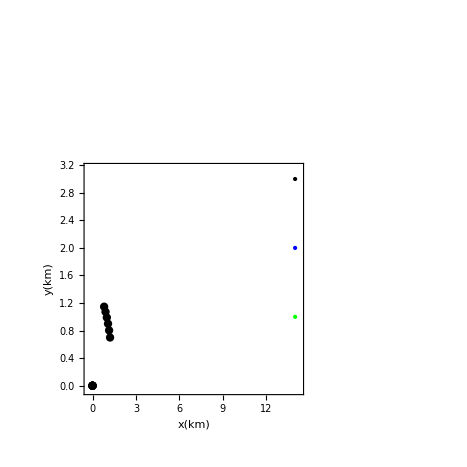

## Problem 4

```mathematica
Clear["Global`*"];
 color = {Black,Blue,Green,Pink,Magenta,Red};  grav = 9.8; tmax = 1000; v0 = 700;B2m =  4.0 10^-5; x0 = 0.0; y0 =0.0; 
θ=π/180.0 {35.};lθ = Length[θ];
p7 = Table[0,{i,lθ }]; (* Trajectory plots for diff angles *)
dt = {0.1};  ldt = Length[dt];

Do[ p5=  Table[0,{i,ldt }]; (* Trajectory plots for diff dt *)
vx0 = v0 Cos[θ[[nθ]]]; vy0 = v0 Sin[θ[[nθ]]];
Do[
tList = Range[0,1000,dt[[ndt]]]; lt = Length[tList];
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[
xList[[nt]]   = xList[[nt-1]] + vxList[[nt-1]] dt[[ndt]]; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt-1]] dt[[ndt]];
vNorm                 =  Sqrt[vxList[[nt-1]]^2+vyList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] (1.0 - B2m dt[[ndt]] vNorm);
vyList[[nt]] =vyList[[nt-1]] (1.0 - B2m dt[[ndt]] vNorm) - grav dt[[ndt]];
If[yList[[nt]]>0,nRange = nt] (* time when x = Range, y = 0 *)
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,nRange}];
p5[[ndt]] =ListPlot[xylist/1000.0,PlotStyle->color[[ndt]]],{ndt,Length[dt]}]; p7[[nθ]] =p5,{nθ,Length[θ]};
(*critical density*)
Do[
xList[[nt]]   = xList[[nt-1]] + vxList[[nt-1]] dt[[ndt]]; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt-1]] dt[[ndt]];
vNorm                 =  Sqrt[vxList[[nt-1]]^2+vyList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] (1.0 - B2m× dt[[ndt]] vNorm);
vyList[[nt]] =vyList[[nt-1]] (1.0 - B2m×dt[[ndt]] vNorm) - grav dt[[ndt]];
If[yList[[nt]]>0,nRange = nt] (* time when x = Range, y = 0 *)
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,nRange}];
p5[[ndt]] =ListPlot[xylist/1000.0,PlotStyle->color[[ndt]]],{ndt,Length[dt]}]; p7[[nθ]] =p5,{nθ,Length[θ]}


g2=Graphics[{Black,PointSize[Large],Point[{{8,2}}]}];
g3=Graphics[{Blue,PointSize[Large],Point[{{8,1.5}}]}];
g4=Graphics[{Green,PointSize[Large],Point[{{8,1}}]}];Show[p7,g2,g3,g4, PlotRange->All,Frame -> True,FrameLabel->{Style["x(km)",Large],Style["y(km)",Large]},LabelStyle->20,ImageSize->500 ,AspectRatio->1,Epilog->{Inset[Style["With drag",17] ,{20,9}],Inset[Style["30°",17],{13,3.7}], Inset[Style["35°",17] ,{13,4.8}],Inset[Style["45°",17],{13,7.2}], Inset[Style["dt = 2 s",17],{11,2}]}]
```

```mathematica
(*critical density*)
Clear["Global`*"];
B2m=(0.0039+0.0058/(1+Exp[(vNorm-vvd)/tt]));


 Clear["Global`*"];
 color = {Black,Blue,Green,Pink,Magenta,Red};  grav = 9.8; tmax = 1000; v0 = 700; x0 = 0.0; y0 =0.0; 
θ=π/180.0 {35.};lθ = Length[θ];
p7 = Table[0,{i,lθ }]; (* Trajectory plots for diff angles *)
dt = {0.1};  ldt = Length[dt];

Do[ p5=  Table[0,{i,ldt }]; (* Trajectory plots for diff dt *)
vx0 = v0 Cos[θ]; vy0 = v0 Sin[θ];
Do[
tList = Range[0,1000,dt[[ndt]]]; lt = Length[tList];
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[
xList[[nt]]   = xList[[nt-1]] + vxList[[nt-1]] dt[[ndt]]; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt-1]] dt[[ndt]];
vNorm                 =  Sqrt[vxList[[nt-1]]^2+vyList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] (1.0 - (0.0039+0.0058/(1+Exp[(vNorm-vd)/tt])Abs[vNorm-vd](1-vd))× dt[[ndt]] );
vyList[[nt]] =vyList[[nt-1]] (1.0 - (0.0039+0.0058/(1+Exp[(vNorm-vd)/tt]))Abs[vNorm-vd]×dt[[ndt]] ) - grav dt[[ndt]];
If[yList[[nt]]>0,nRange = nt] (* time when x = Range, y = 0 *)
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,nRange}];
p5[[ndt]] =ListPlot[xylist/1000.0,PlotStyle->color[[ndt]]],{ndt,Length[dt]}];p7[[nθ]] =p5,{nθ,Length[θ]}]


g2=Graphics[{Black,PointSize[Large],Point[{{8,2}}]}];
g3=Graphics[{Blue,PointSize[Large],Point[{{8,1.5}}]}];
g4=Graphics[{Green,PointSize[Large],Point[{{8,1}}]}];Show[p7,g2,g3,g4, PlotRange->All,Frame -> True,FrameLabel->{Style["x(km)",Large],Style["y(km)",Large]},LabelStyle->20,ImageSize->500 ,AspectRatio->1,Epilog->{Inset[Style["With drag",17] ,{20,9}],Inset[Style["30°",17],{13,3.7}], Inset[Style["35°",17] ,{13,4.8}],Inset[Style["40°",17] ,{13,6}],Inset[Style["45°",17],{13,7.2}], Inset[Style["50°",17] ,{13,8.2}],Inset[Style["55°",17] ,{12.,9.3}],Inset[Style["dt = 2 s",17],{11,2}], Inset[Style["dt = 0.2 s",17] ,{11,1.5}],Inset[Style["dt = 0.1 s",17] ,{11,1}]}]
```